```mathematica
β[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=
β[ω,δ,t,ϵ1,ϵ2,m]=ReplacePart[ReplacePart[ReplacePart[0*IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t],Table[{a,a},{a,1,2m,2}]->ω+ⅈ*δ-ϵ1],Table[{b,b},{b,2,2m,2}]->ω+ⅈ*δ-ϵ2]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[leads,SR]
```

```mathematica
leads= Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/hBN/leads/lead_right_1_0.75_hbn_"<>ToString[ω]<>".dat"]],{ω,Range[-3.5,3.5,0.01]}]
```

$Aborted

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=LEFT[ω,δ,t,ϵ1,ϵ2,m]=(*leads[[Round[ω*100+351]]]*)Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Inverse[β[ω,δ,t,ϵ1,ϵ2,m]]
SR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ1,ϵ2,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ1,ϵ2,m].T1[t,m]].g[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].SR[ω,δ,t,ϵ2,ϵ1,m].ConjugateTranspose[ρ[t,m]]].SL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]].SR[ω,δ,t,ϵ2,ϵ1,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IL[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IL[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IR[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IR[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].IL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
pris[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].grr[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m]]]
```

```mathematica
pris[2,0.001,1,-0.5,0.5,9]
```

2.99999

```mathematica
pri= Monitor[Table[{ω,pris[ω,0.001,0.6,0.5,0.85,9]},{ω,Range[-1.2,2.6,0.01]}],ω]
```

{{-1.2,0.0000163757},{-1.19,0.0000192428},{-1.18,0.0000229554},{-1.17,0.0000278874},{-1.16,0.0000346457},{-1.15,0.0000442694},{-1.14,0.0000586588},{-1.13,0.0000815995},{-1.12,0.000121541},{-1.11,0.000200656},{-1.1,0.000393672},{-1.09,0.00109764},{-1.08,0.00980066},{-1.07,0.990379},{-1.06,0.998885},{-1.05,0.999599},{-1.04,0.999799},{-1.03,0.999884},{-1.02,0.999929},{-1.01,0.999957},{-1.,0.999977},{-0.99,0.999994},{-0.98,1.00001},{-0.97,1.00003},{-0.96,1.00006},{-0.95,1.0001},{-0.94,1.00019},{-0.93,1.00039},{-0.92,1.00116},{-0.91,1.01203},{-0.9,1.99198},{-0.89,1.99894},{-0.88,1.9996},{-0.87,1.99979},{-0.86,1.99987},{-0.85,1.99991},{-0.84,1.99994},{-0.83,1.99995},{-0.82,1.99996},{-0.81,1.99997},{-0.8,1.99998},{-0.79,1.99998},{-0.78,1.99999},{-0.77,1.99999},{-0.76,2.},{-0.75,2.},{-0.74,2.00001},{-0.73,2.00002},{-0.72,2.00003},{-0.71,2.00004},{-0.7,2.00006},{-0.69,2.00009},{-0.68,2.00016},{-0.67,2.0003},{-0.66,2.00075},{-0.65,2.00384},{-0.64,2.948},{-0.63,2.99825},{-0.62,2.99947},{-0.61,2.99974},{-0.6,2.99985},{-0.59,2.9999},{-0.58,2.99993},{-0.57,2.99994},{-0.56,2.99996},{-0.55,2.99997},{-0.54,2.99997},{-0.53,2.99998},{-0.52,2.99998},{-0.51,2.99998},{-0.5,2.99999},{-0.49,2.99999},{-0.48,2.99999},{-0.47,2.99999},{-0.46,3.},{-0.45,3.},{-0.44,3.},{-0.43,3.00001},{-0.42,3.00001},{-0.41,3.00001},{-0.4,3.00002},{-0.39,3.00003},{-0.38,3.00004},{-0.37,3.00006},{-0.36,3.0001},{-0.35,3.00016},{-0.34,3.0003},{-0.33,3.00072},{-0.32,3.00339},{-0.31,3.91312},{-0.3,3.9981},{-0.29,3.99945},{-0.28,3.99974},{-0.27,3.99985},{-0.26,3.9999},{-0.25,3.99993},{-0.24,3.99994},{-0.23,3.99995},{-0.22,3.99996},{-0.21,3.99997},{-0.2,3.99997},{-0.19,3.99997},{-0.18,3.99998},{-0.17,3.99998},{-0.16,3.99998},{-0.15,3.99998},{-0.14,3.99998},{-0.13,3.99998},{-0.12,3.99998},{-0.11,3.99998},{-0.1,3.99998},{-0.09,3.99998},{-0.08,3.99998},{-0.07,3.99998},{-0.06,3.99998},{-0.05,3.99998},{-0.04,3.99998},{-0.03,3.99998},{-0.02,3.99997},{-0.01,3.99997},{0.,3.99997},{0.01,3.99996},{0.02,3.99995},{0.03,3.99994},{0.04,3.99993},{0.05,3.99991},{0.06,3.99987},{0.07,3.99979},{0.08,3.99961},{0.09,3.99902},{0.1,3.99346},{0.11,3.01596},{0.12,3.00127},{0.13,3.00041},{0.14,3.00019},{0.15,3.0001},{0.16,3.00006},{0.17,3.00003},{0.18,3.},{0.19,2.99998},{0.2,2.99996},{0.21,2.99993},{0.22,2.99989},{0.23,2.9998},{0.24,2.9996},{0.25,2.99889},{0.26,2.99013},{0.27,2.00955},{0.28,2.00109},{0.29,2.00038},{0.3,2.00018},{0.31,2.0001},{0.32,2.00004},{0.33,2.},{0.34,1.99995},{0.35,1.99988},{0.36,1.99972},{0.37,1.9992},{0.38,1.99467},{0.39,1.02129},{0.4,1.0015},{0.41,1.00049},{0.42,1.00021},{0.43,1.00005},{0.44,0.99989},{0.45,0.999555},{0.46,0.997994},{0.47,0.798175},{0.48,0.00303342},{0.49,0.000767365},{0.5,0.000367935},{0.51,0.00022758},{0.52,0.000161236},{0.53,0.000124157},{0.54,0.000101089},{0.55,0.0000856416},{0.56,0.0000747399},{0.57,0.0000667455},{0.58,0.000060717},{0.59,0.0000560805},{0.6,0.0000524693},{0.61,0.0000496403},{0.62,0.0000474278},{0.63,0.0000457169},{0.64,0.0000444271},{0.65,0.0000435024},{0.66,0.0000429052},{0.67,0.0000426121},{0.68,0.0000426121},{0.69,0.0000429052},{0.7,0.0000435024},{0.71,0.0000444271},{0.72,0.0000457169},{0.73,0.0000474278},{0.74,0.0000496403},{0.75,0.0000524693},{0.76,0.0000560805},{0.77,0.000060717},{0.78,0.0000667455},{0.79,0.0000747399},{0.8,0.0000856416},{0.81,0.000101089},{0.82,0.000124157},{0.83,0.000161236},{0.84,0.00022758},{0.85,0.000367935},{0.86,0.000767365},{0.87,0.00303342},{0.88,0.798175},{0.89,0.997994},{0.9,0.999555},{0.91,0.99989},{0.92,1.00005},{0.93,1.00021},{0.94,1.00049},{0.95,1.0015},{0.96,1.02129},{0.97,1.99467},{0.98,1.9992},{0.99,1.99972},{1.,1.99988},{1.01,1.99995},{1.02,2.},{1.03,2.00004},{1.04,2.0001},{1.05,2.00018},{1.06,2.00038},{1.07,2.00109},{1.08,2.00955},{1.09,2.99013},{1.1,2.99889},{1.11,2.9996},{1.12,2.9998},{1.13,2.99989},{1.14,2.99993},{1.15,2.99996},{1.16,2.99998},{1.17,3.},{1.18,3.00003},{1.19,3.00006},{1.2,3.0001},{1.21,3.00019},{1.22,3.00041},{1.23,3.00127},{1.24,3.01596},{1.25,3.99346},{1.26,3.99902},{1.27,3.99961},{1.28,3.99979},{1.29,3.99987},{1.3,3.99991},{1.31,3.99993},{1.32,3.99994},{1.33,3.99995},{1.34,3.99996},{1.35,3.99997},{1.36,3.99997},{1.37,3.99997},{1.38,3.99998},{1.39,3.99998},{1.4,3.99998},{1.41,3.99998},{1.42,3.99998},{1.43,3.99998},{1.44,3.99998},{1.45,3.99998},{1.46,3.99998},{1.47,3.99998},{1.48,3.99998},{1.49,3.99998},{1.5,3.99998},{1.51,3.99998},{1.52,3.99998},{1.53,3.99998},{1.54,3.99997},{1.55,3.99997},{1.56,3.99997},{1.57,3.99996},{1.58,3.99995},{1.59,3.99994},{1.6,3.99993},{1.61,3.9999},{1.62,3.99985},{1.63,3.99974},{1.64,3.99945},{1.65,3.9981},{1.66,3.91312},{1.67,3.00339},{1.68,3.00072},{1.69,3.0003},{1.7,3.00016},{1.71,3.0001},{1.72,3.00006},{1.73,3.00004},{1.74,3.00003},{1.75,3.00002},{1.76,3.00001},{1.77,3.00001},{1.78,3.00001},{1.79,3.},{1.8,3.},{1.81,3.},{1.82,2.99999},{1.83,2.99999},{1.84,2.99999},{1.85,2.99999},{1.86,2.99998},{1.87,2.99998},{1.88,2.99998},{1.89,2.99997},{1.9,2.99997},{1.91,2.99996},{1.92,2.99994},{1.93,2.99993},{1.94,2.9999},{1.95,2.99985},{1.96,2.99974},{1.97,2.99947},{1.98,2.99825},{1.99,2.948},{2.,2.00384},{2.01,2.00075},{2.02,2.0003},{2.03,2.00016},{2.04,2.00009},{2.05,2.00006},{2.06,2.00004},{2.07,2.00003},{2.08,2.00002},{2.09,2.00001},{2.1,2.},{2.11,2.},{2.12,1.99999},{2.13,1.99999},{2.14,1.99998},{2.15,1.99998},{2.16,1.99997},{2.17,1.99996},{2.18,1.99995},{2.19,1.99994},{2.2,1.99991},{2.21,1.99987},{2.22,1.99979},{2.23,1.9996},{2.24,1.99894},{2.25,1.99198},{2.26,1.01203},{2.27,1.00116},{2.28,1.00039},{2.29,1.00019},{2.3,1.0001},{2.31,1.00006},{2.32,1.00003},{2.33,1.00001},{2.34,0.999994},{2.35,0.999977},{2.36,0.999957},{2.37,0.999929},{2.38,0.999884},{2.39,0.999799},{2.4,0.999599},{2.41,0.998885},{2.42,0.990379},{2.43,0.00980066},{2.44,0.00109764},{2.45,0.000393672},{2.46,0.000200656},{2.47,0.000121541},{2.48,0.0000815995},{2.49,0.0000586588},{2.5,0.0000442694},{2.51,0.0000346457},{2.52,0.0000278874},{2.53,0.0000229554},{2.54,0.0000192428},{2.55,0.0000163757},{2.56,0.0000141137},{2.57,0.0000122963},{2.58,0.0000108131},{2.59,9.58615×10^-6},{2.6,8.55902×10^-6}}

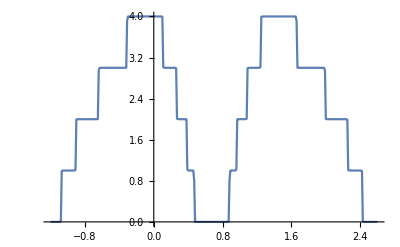

```mathematica
ListPlot[pri,Joined->True]
```

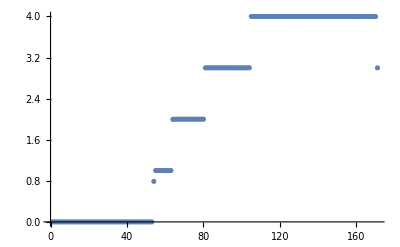

```mathematica
ListPlot[pri]
```

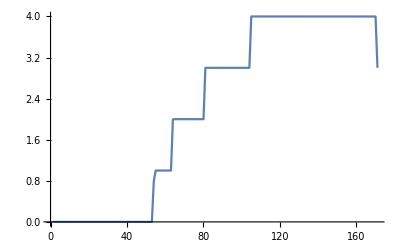

```mathematica
Monitor[ListLinePlot[Table[pris[ω,0.0001,1,-0.5,0.5,9],{ω,Range[0,1.7,0.01]}]],ω]
```

```mathematica
list[num_]:=Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-num],Table[RandomChoice[Range[1,18,1]],num]]]}]]
```

```mathematica
Clear[dist]
```

```mathematica
dist[num_]:=dist[num]=Table[list[num],5000]
```

```mathematica
dist[20][[1]]
```

{{1,0},{2,0},{3,0},{4,0},{5,1},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,1},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,14},{22,3},{23,3},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,10},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,2},{44,0},{45,0},{46,0},{47,9},{48,2},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,7},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,6},{64,0},{65,0},{66,0},{67,0},{68,8},{69,0},{70,0},{71,8},{72,0},{73,0},{74,0},{75,0},{76,0},{77,10},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,13},{91,1},{92,0},{93,12},{94,0},{95,0},{96,0},{97,17},{98,3},{99,14},{100,0}}

```mathematica
device[ω_,δ_,ϵ_,m_,number_,conc_]:=Module[{},
sl1= Module[{J=SL[ω,0.001,0.6,0.5,0.85,m]},Do[J=Inverse[IdentityMatrix[2m]-Inverse[Module[{κ=β[ω,0.001,0.6,0.5,0.85,m],n= dist[conc][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ]]].ConjugateTranspose[T1[1,m]].J.T1[1,m]].Inverse[Module[{κ=β[ω,0.001,0.6,0.5,0.85,m],n= dist[conc][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ]]],{loc1,100}];
 J=J];
il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,0.001,0.6,0.85,0.5,m].ConjugateTranspose[ρ[1,m]]].sl1;
ir1:=Inverse[IdentityMatrix[2m]-SR[ω,0.001,0.6,0.85,0.5,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,0.001,0.6,0.85,0.5,m];gdd1:=il1-ConjugateTranspose[il1];grr1:= ir1-ConjugateTranspose[ir1];Gnonlocal1:= SR[ω,0.001,0.6,0.85,0.5,m].ρ[1,m].il1;GNON1:=Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];If[tr1>pris[ω,0.001,0.6,0.5,0.85,9],pris[ω,0.001,0.6,0.5,0.85,9],tr1]]
```

```mathematica
Clear[f]
```

```mathematica
f[num_,conc_]:= f[num,conc]= Monitor[Table[{ω,device[ω,0.001,0,9,num,conc]},{ω,Range[-1.2,2.6,0.01]}],ω]
```

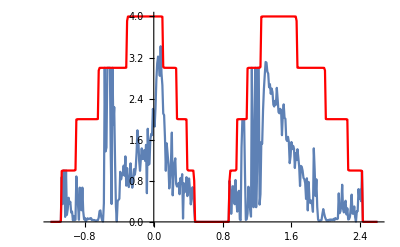

```mathematica
Show[ListLinePlot[f[4,20]],ListLinePlot[pri,PlotStyle->Red],PlotRange->All]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/hbn_trans.dat",f[4,20]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/hbn_trans.dat

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/hbn_trans_pris.dat",f[4,0]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/hbn_trans_pris.dat

```mathematica
ListPlot[%34]
```

```mathematica
Monitor[Table[Table[f[n,conc],{n,50}],{conc,0,70,5}],{n,conc}]
```

```mathematica
Dimensions[%48]
```

{15,50,171}

```mathematica
NIntegrate[Interpolation[pri][x],{x,1.,170.}]
```

```mathematica
Monitor[Table[Table[NIntegrate[Interpolation[%48[[conc]][[n]]][x],{x,1.,170.}],{n,50}],{conc,15}],{conc,n}]/NIntegrate[Interpolation[pri][x],{x,1.,170.}]
```

```mathematica
Table[Around[%52[[x]]],{x,15}]
```

{1.00001,0.9290.006,0.8730.008,0.8290.007,0.7930.009,0.7610.010,0.7310.009,0.7040.009,0.6820.011,0.6600.012,0.6400.010,0.6250.012,0.6080.011,0.5930.012,0.5830.009}

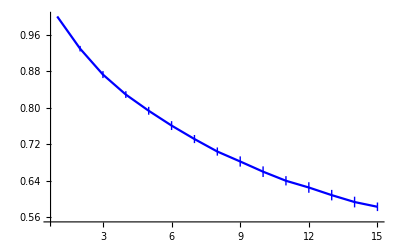

```mathematica
ListLinePlot[Table[Around[%52[[x]]],{x,15}],PlotRange->All,PlotStyle->Blue]
```

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,10],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_vac.dat",Transpose[Join[{Range[-3,3,0.01]},{%30}]]]
```

/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_vac.dat

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,20],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

{0.000643647,0.000837803,0.00121894,0.00176292,0.00267671,0.0053008,0.0790042,0.0737028,0.0733371,0.0752728,0.0775939,0.0758953,0.0804314,0.0803879,0.0904952,0.0860247,0.0847096,0.088845,0.092452,0.0922718,0.099062,0.0992219,0.102523,0.106929,0.117906,0.116366,0.130951,0.135147,0.140003,0.148038,0.167796,0.171383,0.184689,0.202418,0.338959,0.286003,0.239676,0.222834,0.196345,0.186192,0.17019,0.165321,0.157991,0.160617,0.16247,0.155047,0.160792,0.1484,0.152107,0.146437,0.144617,0.149088,0.1505,0.151492,0.168566,0.153282,0.162734,0.163501,0.150253,0.168802,0.166606,0.171508,0.1738,0.177573,0.174049,0.181108,0.184891,0.195529,0.193803,0.198701,0.196609,0.208555,0.219219,0.226043,0.250778,0.290474,0.379491,1.76913,0.851479,0.571067,0.485635,0.411279,0.378235,0.33989,0.326516,0.297728,0.282873,0.268148,0.256743,0.255512,0.257895,0.246033,0.251755,0.24719,0.248055,0.243778,0.244594,0.246076,0.247782,0.239077,0.238615,0.252326,0.249344,0.241208,0.247071,0.244465,0.253909,0.252191,0.266527,0.264057,0.281079,0.280951,0.276037,0.285048,0.287635,0.293713,0.298251,0.294654,0.304057,0.305489,0.315554,0.31618,0.337126,0.321149,0.34165,0.361638,0.3803,0.412836,0.477557,0.629386,0.885519,3.03259,1.87395,1.53678,1.2112,1.02303,0.905245,0.816994,0.772294,0.739504,0.673448,0.578143,0.596205,0.574833,0.545985,0.533631,0.507441,0.466552,0.476872,0.469025,0.464193,0.428585,0.446295,0.442134,0.420809,0.408048,0.419757,0.419024,0.400728,0.39744,0.400252,0.407471,0.403168,0.398961,0.410028,0.401655,0.411067,0.404985,0.395338,0.39804,0.397561,0.373271,0.364027,0.364981,0.39421,0.401308,0.40846,0.393281,0.402516,0.402349,0.412165,0.477155,0.559797,0.626388,0.760549,0.851501,0.957197,1.04733,1.05439,1.06687,0.984922,0.916711,0.835355,0.756879,0.692692,0.647403,0.686789,0.776394,0.837316,0.785361,0.722597,0.661719,0.61296,0.577289,0.568254,0.540411,0.501776,0.495025,0.505249,0.50849,0.476454,0.519562,0.537009,0.567965,0.634661,0.664262,0.728528,0.827561,1.02131,1.2915,1.87869,0.922926,0.611197,0.507115,0.469595,0.468779,0.426562,0.47924,0.492224,0.494654,0.512394,0.553717,0.630669,0.663923,0.826045,0.92148,1.0676,1.36108,0.62442,1.53605,1.7613,10.2818,1.89202,2.00685,1.48693,0.574754,0.411022,2.64367,1.59083,0.179064,0.0330516,0.0261028,0.0200936,0.0160727,0.0153414,0.0134588,0.0112643,0.00981221,0.0101784,0.00874324,0.00768275,0.00755646,0.00681167,0.00603429,0.0061032,0.00540714,0.00569567,0.00520708,0.00470502,0.0045861,0.00449088,0.00404179,0.00426221,0.00387993,0.00379282,0.00352049,0.00343119,0.00359694,0.00306297,0.00345236,0.00332994,0.00287625,0.00308642,0.00294906,0.0027819,0.00277943,0.00270013,0.00260893,0.00262366,0.00265957,0.0024783,0.00267838,0.00259334,0.00248369,0.00248722,0.00241914,0.00258168,0.00242574,0.00254604,0.00250779,0.00243686,0.00242874,0.00264336,0.00250261,0.0026614,0.00246595,0.00254371,0.00256253,0.00265039,0.00273536,0.00255208,0.00281831,0.002571,0.00259422,0.00263603,0.00288378,0.0027487,0.00309628,0.00293592,0.00306131,0.00324166,0.00318186,0.00325466,0.00328767,0.0033617,0.00369156,0.00359739,0.00393985,0.00403106,0.00424868,0.00445596,0.00484913,0.00471367,0.00503576,0.00560087,0.00568543,0.00616668,0.00670821,0.00660132,0.00726481,0.00771038,0.00856384,0.00872588,0.00987026,0.0111517,0.0130176,0.0144789,0.0180615,0.0189171,0.0237868,0.0826818,0.173858,2.10549,2.48484,0.500985,0.481648,1.19126,2.89513,1.99626,7.71781,1.86349,0.735146,0.887156,1.36165,1.13624,0.966621,0.832531,0.683374,0.60088,0.596845,0.522536,0.486835,0.471433,0.466793,0.470276,0.454672,0.48694,0.488153,0.611141,0.897695,1.90819,1.29197,1.0219,0.820303,0.743,0.659086,0.625204,0.582597,0.549811,0.525692,0.498275,0.506095,0.504033,0.513894,0.491363,0.53374,0.58921,0.577344,0.624124,0.679475,0.698894,0.793342,0.827263,0.81268,0.682292,0.639941,0.694224,0.763465,0.828412,0.912766,0.996478,1.06848,1.06279,1.03656,0.945679,0.861049,0.754047,0.620867,0.544256,0.487116,0.417519,0.406113,0.397128,0.401064,0.411924,0.406676,0.400571,0.360463,0.366007,0.384971,0.384285,0.385841,0.397637,0.407954,0.400468,0.402774,0.403142,0.401248,0.405277,0.403998,0.399189,0.398097,0.395409,0.418688,0.412957,0.421387,0.416237,0.43433,0.447427,0.424714,0.461264,0.47448,0.480809,0.462164,0.511496,0.539089,0.539633,0.587018,0.588287,0.583281,0.672215,0.74248,0.768328,0.844344,0.909372,1.02792,1.21354,1.52898,1.87196,3.09387,0.972783,0.633341,0.465792,0.41424,0.379141,0.363245,0.354049,0.32227,0.326741,0.319738,0.313626,0.311652,0.3126,0.288366,0.29516,0.288456,0.297213,0.280625,0.280132,0.277213,0.278768,0.270272,0.270016,0.248206,0.25713,0.243507,0.245513,0.240553,0.254435,0.250597,0.241068,0.241973,0.23816,0.244273,0.247045,0.249027,0.248326,0.241803,0.241292,0.255361,0.257961,0.260783,0.260045,0.273223,0.27754,0.296122,0.321693,0.339083,0.376387,0.416124,0.498656,0.579178,0.803579,1.79053,0.380937,0.275899,0.24507,0.23295,0.221836,0.204494,0.20076,0.197183,0.194061,0.195292,0.18311,0.170864,0.180039,0.178058,0.176481,0.170403,0.164294,0.158272,0.155342,0.158246,0.154568,0.147352,0.161079,0.145256,0.153765,0.146191,0.144111,0.145316,0.155114,0.149934,0.153091,0.15541,0.158803,0.161078,0.15671,0.161696,0.170655,0.181515,0.203385,0.217982,0.236945,0.270208,0.329866,0.212761,0.185129,0.170988,0.161869,0.151114,0.144701,0.13295,0.131441,0.119596,0.122469,0.107707,0.103301,0.100301,0.100958,0.0952794,0.0870446,0.0913877,0.085459,0.082321,0.0845878,0.0808683,0.0810826,0.0766231,0.0786562,0.076491,0.0738019,0.0822493,0.077118,0.00601857,0.0030206,0.00176532,0.00120285,0.000868233,0.000693006}

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,30],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

{0.000953161,0.0013257,0.00170008,0.00259821,0.00391993,0.00773592,0.0550422,0.061589,0.0632867,0.0650178,0.0674386,0.0643895,0.068805,0.0700463,0.0721127,0.0705639,0.0726311,0.0785417,0.0732838,0.0705566,0.0756778,0.0777487,0.0791502,0.0859164,0.0911534,0.0921996,0.0934065,0.101921,0.102088,0.116759,0.123143,0.133408,0.152609,0.191777,0.327429,0.278827,0.226077,0.200483,0.181782,0.169298,0.157162,0.145884,0.138294,0.12922,0.135571,0.12319,0.116812,0.116751,0.115663,0.107902,0.108256,0.109016,0.10701,0.105867,0.109895,0.105104,0.11253,0.108286,0.104643,0.110283,0.119425,0.111681,0.114283,0.120146,0.119715,0.115591,0.121397,0.130764,0.137319,0.131719,0.137877,0.138956,0.154708,0.171761,0.194862,0.257378,0.421597,1.94646,0.933114,0.673147,0.545302,0.451503,0.418304,0.35363,0.340427,0.309085,0.28506,0.289335,0.260743,0.245764,0.244664,0.222147,0.223868,0.223186,0.218609,0.213712,0.205825,0.208288,0.205641,0.196228,0.205713,0.191253,0.197174,0.187239,0.187123,0.200227,0.192074,0.186431,0.196556,0.204891,0.20094,0.195857,0.207008,0.204699,0.212398,0.203212,0.206679,0.207703,0.208812,0.210316,0.223515,0.231395,0.239645,0.248567,0.272543,0.289101,0.305952,0.35638,0.459317,0.660801,1.22621,3.61078,2.23273,1.87359,1.45421,1.26452,1.0643,1.00174,0.916204,0.91961,0.810919,0.748547,0.719556,0.720732,0.690295,0.688725,0.641225,0.594937,0.596076,0.600837,0.583689,0.526582,0.538275,0.528995,0.517972,0.501646,0.504155,0.508815,0.48861,0.472623,0.480354,0.498353,0.508628,0.484338,0.501015,0.502822,0.484464,0.493617,0.492554,0.491872,0.465948,0.434969,0.358412,0.401553,0.457423,0.491913,0.485316,0.484667,0.464106,0.449927,0.400902,0.367221,0.403666,0.44009,0.520735,0.628228,0.716439,0.804145,0.814212,0.812505,0.737155,0.640227,0.567105,0.516536,0.497327,0.519347,0.684939,0.903138,0.700937,0.663901,0.645417,0.644034,0.629842,0.628213,0.621704,0.602482,0.613752,0.632026,0.630808,0.615023,0.634145,0.658676,0.659616,0.718704,0.765746,0.81037,0.889848,1.01495,1.12781,1.37205,1.98446,1.1931,0.789247,0.666099,0.597753,0.626825,0.583753,0.608328,0.614178,0.615666,0.685277,0.746494,0.776959,0.873923,1.00449,1.1,1.4203,1.55917,1.37741,1.81806,4.19538,4.67766,2.69864,4.80248,4.48699,6.20049,0.698344,5.56928,1.87306,0.38309,0.0580028,0.0368999,0.0318354,0.0252832,0.0210849,0.0192548,0.0168441,0.015716,0.0147436,0.0127992,0.0116456,0.011478,0.0100331,0.0094714,0.00935072,0.0088693,0.00773493,0.00768323,0.00745584,0.00681575,0.00665361,0.00641411,0.00599925,0.0060153,0.0054178,0.0048821,0.00550885,0.00509776,0.00492934,0.00441398,0.00439181,0.00444845,0.00441231,0.00467773,0.00427089,0.00416312,0.00431437,0.00434171,0.00369445,0.0041214,0.00387229,0.00402885,0.00381493,0.00379164,0.00393098,0.00384052,0.00381109,0.00382399,0.00352387,0.00373974,0.0036212,0.00378214,0.00380762,0.00368573,0.00376135,0.00386067,0.00364447,0.00389319,0.00378854,0.00396504,0.0038319,0.00382764,0.00410516,0.00392408,0.00431007,0.00432637,0.00436016,0.00442364,0.00416497,0.00476512,0.00473131,0.00475372,0.00511466,0.00492163,0.0049017,0.00557242,0.00545354,0.00553071,0.0059023,0.00614736,0.00609633,0.00669506,0.00735204,0.00768217,0.00760492,0.00838095,0.00867262,0.0098521,0.010136,0.0114813,0.0116475,0.0131824,0.0146907,0.0158967,0.0173403,0.0196497,0.021755,0.026799,0.0300478,0.0371437,0.124373,0.488941,1.38072,5.7115,0.727563,0.757199,3.2316,7.22598,2.47021,4.92023,2.35665,1.2723,1.06869,1.6449,1.3541,1.13693,0.997159,0.878612,0.759556,0.745313,0.671928,0.653514,0.625292,0.573153,0.585801,0.608195,0.631322,0.639851,0.7933,1.19329,1.99839,1.39782,1.16171,0.992111,0.885029,0.825049,0.755211,0.686831,0.698733,0.66402,0.62389,0.640666,0.60294,0.627175,0.611424,0.587062,0.632809,0.626719,0.624921,0.661089,0.664645,0.674671,0.708977,0.880716,0.688026,0.515736,0.486856,0.524141,0.578031,0.640898,0.74657,0.812389,0.812404,0.799302,0.71631,0.631619,0.521348,0.436642,0.392887,0.376722,0.401304,0.438952,0.465694,0.479816,0.485083,0.482544,0.454491,0.393625,0.371944,0.437578,0.474327,0.476251,0.472507,0.485411,0.489429,0.491891,0.486263,0.486458,0.494537,0.508245,0.492544,0.486824,0.473742,0.505921,0.491318,0.50904,0.519664,0.531507,0.546773,0.522566,0.578003,0.595644,0.589719,0.581309,0.637732,0.690226,0.676955,0.709571,0.720722,0.743026,0.813995,0.923825,0.93233,1.00243,1.0757,1.29266,1.47447,1.79622,2.2285,3.60442,1.21393,0.656512,0.443596,0.35845,0.315352,0.291301,0.268654,0.249278,0.230142,0.232219,0.225322,0.212577,0.212922,0.212034,0.210881,0.209012,0.209059,0.212054,0.205607,0.198057,0.204313,0.201346,0.197143,0.186913,0.193055,0.199116,0.186226,0.186121,0.1944,0.191908,0.20682,0.199631,0.199316,0.208947,0.209625,0.215996,0.223138,0.223456,0.224841,0.228414,0.243105,0.254455,0.264866,0.285301,0.290102,0.298361,0.333426,0.363027,0.408947,0.450199,0.534472,0.681893,0.927798,1.98955,0.413214,0.245326,0.195698,0.168204,0.151653,0.140134,0.13849,0.132684,0.127407,0.130368,0.118956,0.113862,0.121573,0.112758,0.11298,0.114294,0.11524,0.109538,0.0999478,0.1053,0.113127,0.101485,0.106152,0.109783,0.107502,0.110048,0.106767,0.110361,0.113912,0.119439,0.120308,0.121204,0.128561,0.12809,0.140537,0.1443,0.159373,0.167779,0.180045,0.200465,0.225119,0.272445,0.324388,0.183663,0.154702,0.133654,0.122453,0.119427,0.10557,0.0975124,0.0943086,0.0952888,0.098619,0.0829794,0.0823744,0.080681,0.077135,0.0731205,0.0769542,0.0747071,0.0743647,0.0698664,0.0739063,0.0724167,0.0704655,0.0685438,0.0663893,0.0666978,0.0654285,0.0656601,0.0569153,0.00774806,0.00386253,0.0024493,0.00165705,0.00138522,0.000979948}

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,40],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

{0.00122529,0.0016923,0.00228958,0.0032101,0.00474403,0.00956659,0.0463537,0.0583053,0.0596909,0.0592821,0.0616,0.0659972,0.0632276,0.0703156,0.0657961,0.0632097,0.0683709,0.0677188,0.0707199,0.0746407,0.076682,0.0735681,0.0802952,0.0848673,0.0840661,0.0881414,0.0901611,0.0898642,0.0993042,0.107612,0.106575,0.123831,0.14488,0.197961,0.325814,0.256674,0.234952,0.205839,0.186099,0.161361,0.146506,0.139443,0.134908,0.120655,0.122055,0.112585,0.111553,0.103274,0.104315,0.0985467,0.101958,0.096342,0.0938585,0.0965171,0.0998066,0.0975295,0.0885814,0.0872003,0.0892935,0.090417,0.0978495,0.0873033,0.0971714,0.0958924,0.105357,0.10049,0.103188,0.112598,0.111816,0.117888,0.12412,0.128512,0.143513,0.169052,0.188504,0.266887,0.488006,1.88148,0.996205,0.709764,0.609122,0.484632,0.434479,0.39625,0.370243,0.324205,0.293752,0.295569,0.274382,0.26457,0.247808,0.240138,0.235678,0.235829,0.225028,0.22106,0.204959,0.207135,0.202218,0.189245,0.198662,0.187158,0.186835,0.180283,0.191801,0.187942,0.18046,0.175625,0.177238,0.183749,0.179046,0.181454,0.19028,0.186196,0.194489,0.19237,0.190067,0.18765,0.193016,0.199893,0.219953,0.216441,0.225583,0.246205,0.247575,0.299299,0.324333,0.416203,0.508829,0.757445,1.53417,3.74798,2.39628,1.8942,1.56533,1.36376,1.15818,1.12429,1.01568,0.987704,0.916911,0.82198,0.81528,0.836067,0.767551,0.753363,0.722569,0.657553,0.663995,0.675584,0.643277,0.586068,0.609074,0.608932,0.581948,0.585503,0.570516,0.578314,0.563385,0.538588,0.564763,0.572607,0.572265,0.552792,0.551941,0.56714,0.56,0.568102,0.529451,0.545021,0.513146,0.48363,0.397083,0.417217,0.505226,0.522312,0.546382,0.534817,0.519183,0.507726,0.446937,0.398411,0.367775,0.371083,0.432694,0.506757,0.589443,0.650764,0.657408,0.658632,0.592365,0.500896,0.458005,0.441312,0.462841,0.567936,0.838586,1.13535,0.782138,0.79205,0.764332,0.76964,0.791679,0.76553,0.789328,0.737582,0.741015,0.756024,0.782198,0.767996,0.772277,0.766099,0.776422,0.830758,0.928289,0.945568,1.01172,1.15142,1.32328,1.61686,2.20604,1.40393,0.966051,0.866061,0.773456,0.750446,0.775513,0.758463,0.724998,0.750629,0.789808,0.869494,0.96408,1.08803,1.22382,1.42128,1.5581,2.14251,2.58673,1.97792,3.70375,7.74298,2.16995,9.13126,2.79255,1.25814,0.856101,7.52854,1.3646,0.789044,0.0802499,0.0469064,0.0415583,0.0344805,0.0308306,0.0242904,0.0225444,0.0208412,0.0192906,0.0172952,0.0152146,0.0149721,0.0131206,0.0121936,0.0114592,0.0112397,0.0106068,0.0102991,0.00918651,0.00856635,0.00855281,0.0077976,0.00799978,0.00767148,0.00727762,0.00728943,0.00678119,0.00646279,0.00660389,0.00623756,0.00594824,0.00606209,0.00569044,0.00594385,0.00590609,0.005222,0.00557846,0.00549495,0.00534654,0.00527591,0.00527935,0.00528941,0.0052395,0.00491233,0.00501412,0.00508508,0.00501807,0.00481096,0.00477494,0.00494823,0.00470202,0.00491926,0.00488691,0.00504003,0.00493057,0.00496789,0.00511809,0.00497221,0.00520142,0.00504261,0.00494557,0.00521911,0.00520625,0.0053052,0.0056712,0.00542545,0.00594113,0.00580578,0.00566126,0.00597065,0.00594823,0.00643943,0.00655771,0.00670947,0.00713475,0.00737824,0.00765706,0.00767467,0.00766069,0.00803227,0.00846288,0.00875275,0.00918903,0.00947791,0.0108518,0.0115875,0.0119978,0.0128195,0.0134319,0.0147329,0.0148373,0.0172984,0.0181199,0.0206984,0.023481,0.0239928,0.0309241,0.0320168,0.0409517,0.0488088,0.173867,1.09582,2.5362,6.89578,0.885441,1.67936,10.3589,4.95529,2.91984,8.13157,3.2256,2.17911,1.80438,2.05816,1.58731,1.29347,1.3102,1.03829,0.909604,0.846853,0.779281,0.791266,0.745959,0.783723,0.722546,0.692163,0.744742,0.820639,0.996888,1.47813,2.15373,1.6201,1.27012,1.11978,0.988698,0.945821,0.862602,0.827034,0.781957,0.78966,0.758104,0.740879,0.774806,0.750497,0.749301,0.745975,0.792775,0.730923,0.782462,0.783159,0.766073,0.754455,0.797409,1.09636,0.845614,0.56978,0.472848,0.441176,0.466945,0.50006,0.596173,0.650407,0.659145,0.662217,0.592582,0.503595,0.442734,0.376079,0.359959,0.39706,0.443859,0.508371,0.538291,0.539508,0.528962,0.518104,0.49917,0.420642,0.399138,0.481999,0.509982,0.54111,0.539792,0.56689,0.548684,0.570246,0.564161,0.551668,0.574408,0.573291,0.561679,0.538316,0.560313,0.585979,0.569849,0.581089,0.572146,0.605286,0.604194,0.60341,0.639991,0.684825,0.656573,0.663274,0.714934,0.744632,0.75185,0.817103,0.814944,0.85427,0.91877,0.982447,1.03738,1.08127,1.18364,1.36079,1.56498,1.92364,2.40957,3.74696,1.51938,0.699511,0.513132,0.410883,0.327635,0.282612,0.255056,0.243514,0.22249,0.213746,0.218139,0.200857,0.19553,0.191263,0.196053,0.192935,0.188564,0.185116,0.180769,0.183791,0.17683,0.179024,0.170902,0.180612,0.183328,0.185144,0.186948,0.177346,0.183976,0.18778,0.191315,0.194258,0.202152,0.209099,0.199525,0.224006,0.226194,0.237073,0.240328,0.237855,0.249953,0.270847,0.268816,0.294608,0.300903,0.331141,0.356224,0.391452,0.440361,0.503192,0.592143,0.710364,0.979102,1.89013,0.490075,0.26495,0.193922,0.168195,0.146557,0.126739,0.13191,0.115813,0.116325,0.113136,0.107798,0.10406,0.104156,0.0982365,0.098653,0.0968925,0.0941275,0.0897508,0.0965171,0.083439,0.0872256,0.0910383,0.0944032,0.0957744,0.0937849,0.0943269,0.101868,0.0939595,0.101101,0.103171,0.109129,0.114753,0.120605,0.127497,0.139004,0.139919,0.147719,0.162951,0.183595,0.195268,0.232873,0.262741,0.326035,0.198,0.137943,0.120643,0.107912,0.106702,0.100393,0.0898786,0.0893663,0.0923588,0.0869119,0.0811399,0.0774227,0.0772127,0.0766401,0.0744989,0.0702405,0.0703726,0.0689104,0.0643284,0.0636461,0.0678865,0.0634297,0.0672644,0.0597051,0.0633334,0.0608659,0.056393,0.0442356,0.00979696,0.00506972,0.00325409,0.00240644,0.0015891,0.0012262}

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,50],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

{0.0016344,0.00213411,0.00298574,0.00393145,0.00629533,0.0122921,0.040127,0.0528049,0.0613147,0.0649801,0.0644519,0.0667888,0.0628979,0.0725424,0.0716367,0.0711655,0.070895,0.0757928,0.0777171,0.0720226,0.0762716,0.0765807,0.081404,0.0790591,0.0863409,0.0892185,0.0893785,0.0843981,0.103058,0.1072,0.117163,0.129232,0.150784,0.208521,0.322341,0.270335,0.229707,0.207559,0.183035,0.166438,0.151705,0.144225,0.130775,0.126155,0.117175,0.113632,0.106548,0.101485,0.100403,0.0991382,0.0955601,0.0923802,0.0893524,0.0888749,0.0911597,0.0896567,0.0886167,0.0873714,0.0825037,0.08605,0.0853704,0.0877921,0.0900024,0.0894638,0.106099,0.102199,0.105059,0.108517,0.116054,0.115219,0.131458,0.132049,0.15335,0.189169,0.217951,0.303279,0.557209,1.8946,1.02244,0.739354,0.593762,0.517217,0.47095,0.406938,0.383813,0.332936,0.311986,0.30893,0.273895,0.269507,0.249234,0.234622,0.250637,0.236158,0.230269,0.226664,0.196646,0.206131,0.209922,0.197499,0.199476,0.192701,0.191266,0.179635,0.184125,0.191603,0.184806,0.176461,0.178739,0.184009,0.174665,0.171219,0.184045,0.186349,0.189027,0.186138,0.199021,0.200805,0.193036,0.197935,0.214591,0.228175,0.22613,0.254489,0.276022,0.324253,0.370344,0.466085,0.615407,0.895733,1.78217,3.91373,2.54442,2.09683,1.70056,1.45457,1.24583,1.14714,1.08745,1.06393,0.959896,0.902972,0.87759,0.866244,0.815842,0.821039,0.76399,0.700819,0.724231,0.72502,0.699475,0.634327,0.660357,0.640846,0.634861,0.616114,0.605503,0.620377,0.604465,0.580403,0.61294,0.620391,0.633281,0.592174,0.617757,0.624959,0.59984,0.605513,0.593698,0.575452,0.550356,0.511012,0.42971,0.428627,0.500861,0.563767,0.580293,0.590729,0.576536,0.55524,0.484614,0.431745,0.374158,0.348596,0.391509,0.440044,0.505559,0.547153,0.538979,0.558616,0.474534,0.425662,0.411137,0.436851,0.516663,0.692312,1.00136,1.35806,1.0533,0.966976,0.967769,0.973682,0.951685,0.928317,0.911039,0.905225,0.873362,0.8668,0.87628,0.878486,0.848827,0.898601,0.879422,0.909087,0.993792,1.0904,1.1292,1.24679,1.39469,1.61994,2.14284,1.66673,1.18098,1.02839,0.906951,0.931963,0.913354,0.962963,1.00704,0.972879,0.956252,1.047,1.07433,1.23062,1.48716,1.46423,1.70182,3.35981,3.59647,2.67638,4.47149,4.81753,3.29854,9.74458,6.29951,1.60759,1.59535,7.66445,12.0041,0.974449,0.101671,0.0639298,0.0508977,0.0435096,0.037379,0.033531,0.0272669,0.0250341,0.0249285,0.0219116,0.0199829,0.0182738,0.0172123,0.0169462,0.0143303,0.0132559,0.0134613,0.0120084,0.0118492,0.0112945,0.0112127,0.0104805,0.0105062,0.00983071,0.00943964,0.00916248,0.00869374,0.00887279,0.00867283,0.00802041,0.00790411,0.00744795,0.00753759,0.00750268,0.00745765,0.00698793,0.00693812,0.00698863,0.00669995,0.00659423,0.00692603,0.00676937,0.00615436,0.00641997,0.00643528,0.00627322,0.00622429,0.00627599,0.00626512,0.00594648,0.00622958,0.00578522,0.00631014,0.00623711,0.00623172,0.00586494,0.00624368,0.00627062,0.006577,0.00659405,0.00647954,0.00680308,0.00671547,0.00652,0.00716732,0.00702887,0.00708143,0.00744441,0.00771717,0.00763836,0.00835201,0.00815508,0.00826407,0.00865677,0.0087626,0.00875256,0.00963781,0.00982226,0.0105006,0.0105408,0.0108093,0.0116889,0.011259,0.0129218,0.0138374,0.0143361,0.0148171,0.0152219,0.0172956,0.0185125,0.0201966,0.0206455,0.0238449,0.0257771,0.0289864,0.0343401,0.0378648,0.0449858,0.0509023,0.0674272,0.216545,1.01567,12.9419,6.8958,1.53604,4.384,8.52818,9.68363,5.08439,7.14207,3.51457,2.89596,3.17683,2.96572,1.78056,1.45874,1.4162,1.19419,1.08926,1.03621,1.02768,0.987344,0.952492,0.871114,0.903679,0.896867,0.92699,0.970451,1.16335,1.66549,2.13536,1.6601,1.42242,1.22399,1.14978,1.0562,0.998196,0.907117,0.866735,0.883275,0.879643,0.847249,0.87393,0.887519,0.893099,0.880556,0.909219,0.939208,0.948368,0.953754,0.938101,0.960432,1.03307,1.42623,1.0096,0.700449,0.516345,0.449155,0.40975,0.425076,0.491675,0.548846,0.542588,0.545021,0.509459,0.429733,0.386764,0.348651,0.372293,0.414409,0.498151,0.537662,0.576304,0.601045,0.574141,0.552041,0.506073,0.423666,0.420486,0.522898,0.551934,0.587422,0.59506,0.606148,0.582437,0.618334,0.622088,0.595361,0.623917,0.610231,0.613924,0.587303,0.601539,0.636102,0.59954,0.644886,0.630129,0.642818,0.651561,0.631289,0.700782,0.739169,0.728267,0.699515,0.756912,0.792624,0.821404,0.865424,0.848724,0.899559,0.968522,1.05126,1.08896,1.15222,1.28075,1.46382,1.71758,2.05352,2.50998,3.79273,1.77819,0.860657,0.609092,0.460078,0.35759,0.322831,0.268431,0.265526,0.238685,0.225689,0.220471,0.198303,0.202388,0.199621,0.198026,0.184235,0.187821,0.189955,0.185014,0.172961,0.17004,0.182523,0.176655,0.172998,0.18287,0.186798,0.182318,0.174986,0.187369,0.188649,0.197923,0.1962,0.209959,0.206095,0.195477,0.228419,0.226146,0.237385,0.250266,0.24152,0.252191,0.274186,0.28272,0.308271,0.308042,0.336703,0.386922,0.405043,0.475534,0.507813,0.60993,0.746567,1.04779,1.88139,0.550349,0.309081,0.223443,0.1842,0.154308,0.134742,0.125345,0.118032,0.107337,0.107829,0.10186,0.0945124,0.0953975,0.0915448,0.0925719,0.0935294,0.0852067,0.082363,0.0842057,0.0829227,0.0923513,0.0881649,0.0861298,0.088757,0.0920242,0.0932706,0.0943266,0.100378,0.101926,0.101278,0.1047,0.110021,0.113972,0.122762,0.131575,0.142624,0.150222,0.166533,0.181933,0.211935,0.227357,0.263552,0.321233,0.226034,0.14892,0.130118,0.116515,0.104415,0.102425,0.0900858,0.0829982,0.0848625,0.0813985,0.079238,0.0777547,0.0766643,0.0765723,0.0728539,0.0736599,0.0709665,0.0751722,0.0689723,0.0689098,0.0722026,0.0664429,0.0646543,0.0634106,0.0634544,0.0619308,0.0505346,0.0405988,0.0124379,0.0059843,0.00400879,0.00309645,0.00206972,0.00171283}

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,60],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

{0.00196292,0.00247262,0.00336865,0.00472271,0.00770744,0.0146351,0.0387209,0.0457875,0.0533829,0.0697687,0.065264,0.0692065,0.0689991,0.0721824,0.0725506,0.075029,0.0804053,0.0714512,0.0763211,0.0768672,0.0811708,0.0820721,0.0840169,0.0891371,0.0845198,0.0875772,0.0958668,0.0983106,0.107629,0.113874,0.11905,0.138909,0.172366,0.233658,0.322049,0.266621,0.22847,0.205043,0.183879,0.171581,0.15818,0.14017,0.133798,0.125976,0.116606,0.109648,0.100947,0.100385,0.0951345,0.0978004,0.0959268,0.0921767,0.0903686,0.0908272,0.0891562,0.0873113,0.0845344,0.083608,0.0859618,0.0834571,0.0856174,0.0922129,0.0981106,0.0943078,0.0975916,0.104971,0.110395,0.115814,0.120531,0.124786,0.126068,0.145034,0.162636,0.198153,0.251285,0.347303,0.662496,1.79929,1.06193,0.754638,0.644301,0.539786,0.472603,0.429899,0.39612,0.346503,0.32984,0.310859,0.287211,0.284087,0.263447,0.243891,0.246226,0.242383,0.238112,0.230119,0.208596,0.217775,0.215762,0.202739,0.210197,0.201925,0.193928,0.187017,0.195598,0.200302,0.193923,0.179634,0.184016,0.19076,0.178852,0.178483,0.19169,0.198522,0.202601,0.203491,0.202916,0.202139,0.19791,0.208246,0.225542,0.242684,0.244146,0.297224,0.305526,0.37884,0.413755,0.533172,0.690431,1.04956,1.96737,4.03513,2.62188,2.11485,1.74243,1.49767,1.31686,1.22869,1.15454,1.08771,1.01487,0.918342,0.925102,0.914365,0.858394,0.846243,0.812485,0.740165,0.761114,0.771491,0.732145,0.659665,0.704036,0.667388,0.679889,0.655616,0.635898,0.657513,0.64791,0.620835,0.635942,0.65982,0.653679,0.651075,0.65353,0.643421,0.633918,0.664467,0.617463,0.606873,0.571451,0.537558,0.440186,0.439077,0.4946,0.547209,0.582436,0.603968,0.608975,0.576176,0.539571,0.440482,0.386896,0.365863,0.363316,0.409185,0.448256,0.473436,0.471098,0.458529,0.410808,0.377413,0.404076,0.488348,0.595861,0.804305,1.12689,1.57156,1.23507,1.13298,1.12332,1.10152,1.10987,1.08961,1.02253,1.02908,0.963671,0.987014,0.977746,0.97028,0.973614,0.974042,0.984729,1.02755,1.06652,1.14135,1.26454,1.33602,1.55556,1.77262,2.24181,1.70172,1.38768,1.17701,1.13222,1.06635,1.05271,1.11491,1.15029,1.10636,1.12964,1.19481,1.27877,1.37858,1.66689,1.65613,1.82792,2.61634,3.33136,3.45132,7.09841,7.44894,4.0432,13.5014,6.6595,2.46492,1.54224,9.17565,26.4473,2.62773,0.120945,0.0788418,0.0632534,0.0529222,0.0449185,0.0384835,0.034408,0.030744,0.0292163,0.0267262,0.024105,0.0216591,0.0200163,0.01956,0.0184577,0.0168688,0.0157919,0.0152541,0.0145162,0.0140498,0.0137342,0.0122825,0.0126093,0.0114149,0.0115538,0.0105004,0.0106067,0.00984765,0.0101363,0.00970374,0.00933286,0.00908868,0.00852085,0.00946128,0.00896888,0.00838849,0.00838702,0.00849092,0.00844859,0.00829055,0.00777869,0.00758967,0.00786054,0.00747437,0.00766552,0.00731127,0.00779919,0.00745101,0.00717184,0.00743256,0.00716396,0.00725928,0.00753289,0.00730893,0.00735744,0.00770491,0.00761604,0.00752016,0.00750817,0.0075496,0.00830849,0.00829055,0.00797851,0.00816131,0.00807064,0.00840981,0.00816053,0.00909448,0.00874065,0.00917374,0.009724,0.00955483,0.00986848,0.0105685,0.0106105,0.0111601,0.0112853,0.0121479,0.0119833,0.0125449,0.013073,0.0134801,0.0144911,0.0147799,0.0166045,0.0166892,0.0177891,0.019647,0.0209315,0.022477,0.0240183,0.0265915,0.0289268,0.0311908,0.0351497,0.0392665,0.0448497,0.0545863,0.0644531,0.0848157,0.263596,4.19213,8.40673,8.50129,1.6196,3.65445,8.44503,13.3272,4.39592,4.60273,5.47888,3.34506,2.75172,2.71773,1.72875,1.61246,1.69543,1.36885,1.27825,1.19609,1.12635,1.12168,1.08142,1.09157,1.05041,0.998842,1.07177,1.16519,1.32621,1.89427,2.20341,1.81532,1.5218,1.35321,1.2831,1.11421,1.11643,1.04642,1.00786,0.980578,0.94484,0.992478,0.964394,0.954319,0.995347,1.04362,1.02602,1.04764,1.0852,1.13723,1.13164,1.15298,1.22703,1.55768,1.11469,0.766574,0.6024,0.477932,0.406131,0.386499,0.418777,0.462192,0.473292,0.475606,0.457436,0.405328,0.358052,0.366952,0.387448,0.442737,0.520414,0.573206,0.6024,0.613009,0.586305,0.54411,0.506715,0.423911,0.454089,0.537328,0.570243,0.602061,0.620711,0.643946,0.629743,0.637069,0.644881,0.627433,0.652722,0.632864,0.636677,0.62664,0.630084,0.655194,0.63667,0.649142,0.654008,0.674652,0.693332,0.672173,0.714572,0.768259,0.760215,0.736921,0.813762,0.835649,0.845842,0.929986,0.910898,0.941179,1.00531,1.09295,1.17793,1.22009,1.28428,1.53661,1.74157,2.14065,2.64177,4.06377,2.05356,1.03075,0.731055,0.531437,0.433203,0.367887,0.30236,0.283104,0.252685,0.243563,0.233024,0.206647,0.197179,0.201028,0.20339,0.203337,0.20166,0.196884,0.187833,0.185916,0.177805,0.193062,0.180705,0.181573,0.196058,0.194162,0.192868,0.185482,0.201427,0.200516,0.210162,0.205357,0.214096,0.218232,0.209931,0.233369,0.231923,0.244118,0.247115,0.24569,0.266412,0.279029,0.279975,0.314333,0.321798,0.351625,0.410068,0.423885,0.475129,0.528037,0.641657,0.785144,1.07858,1.74037,0.642448,0.34026,0.259581,0.208137,0.166574,0.144181,0.130667,0.124732,0.114583,0.116217,0.108607,0.0985272,0.104329,0.0986,0.0950798,0.0928001,0.0867247,0.087923,0.0814317,0.0859736,0.0832449,0.0915784,0.0870131,0.0907063,0.0944188,0.0912268,0.0951809,0.098444,0.0962717,0.102246,0.104605,0.112706,0.118646,0.127929,0.13018,0.141639,0.155236,0.169657,0.182321,0.208039,0.2345,0.267997,0.334402,0.242569,0.164263,0.144002,0.118407,0.115665,0.103818,0.0974286,0.0915205,0.0892474,0.0881963,0.0871452,0.0860817,0.0820985,0.0725574,0.0798575,0.0814987,0.0742668,0.0780509,0.0756434,0.0749239,0.0743029,0.073927,0.0717592,0.0687989,0.0675113,0.0595751,0.0488012,0.0396539,0.0142869,0.00696375,0.00494626,0.0033863,0.00253055,0.00209541}

```mathematica
Table[Mean[ParallelTable[device[ω,0.0001,1,0,9,num,70],{num,2000}]],{ω,Range[-3,3,0.01]}]
```

{0.00236683,0.00290837,0.00398659,0.00571867,0.00837948,0.0154597,0.0411717,0.0476931,0.0559696,0.0674442,0.0641722,0.0759375,0.0792653,0.0823625,0.07983,0.0827973,0.0808286,0.084198,0.0868467,0.086302,0.0872303,0.0912536,0.0896159,0.0899876,0.0924604,0.0936078,0.0988979,0.105982,0.110778,0.121656,0.129944,0.157729,0.182711,0.25722,0.338863,0.275784,0.236341,0.207052,0.189738,0.174419,0.16099,0.147076,0.138284,0.127564,0.118221,0.116499,0.110412,0.107268,0.103284,0.099594,0.100485,0.0967454,0.0991185,0.0862249,0.0942276,0.0894288,0.0888322,0.0859385,0.0890736,0.0873765,0.0910186,0.0962879,0.100951,0.09525,0.10395,0.100406,0.112583,0.12602,0.12248,0.140346,0.14618,0.159055,0.182125,0.229672,0.288246,0.38263,0.692253,1.63221,1.08821,0.793913,0.674206,0.556088,0.491001,0.426834,0.401969,0.361147,0.335061,0.337136,0.295529,0.28399,0.276901,0.257237,0.266334,0.252943,0.241928,0.242505,0.218246,0.233486,0.228214,0.221824,0.219637,0.207832,0.204877,0.189407,0.207626,0.205776,0.199811,0.191707,0.192643,0.206428,0.194763,0.18727,0.204744,0.20069,0.209802,0.209104,0.218405,0.222515,0.212603,0.219433,0.254449,0.253359,0.279256,0.321787,0.337967,0.423689,0.474038,0.569474,0.778029,1.11805,2.13492,4.01063,2.67479,2.24352,1.75705,1.57633,1.34937,1.2679,1.18574,1.14505,1.02143,0.960327,0.966442,0.949163,0.881742,0.881144,0.818527,0.771012,0.799943,0.800002,0.758171,0.69975,0.719549,0.724897,0.700249,0.679159,0.651887,0.684331,0.649961,0.642708,0.665758,0.681238,0.678753,0.64323,0.654173,0.672848,0.64299,0.669265,0.61986,0.604517,0.59083,0.542075,0.457119,0.421098,0.495949,0.550059,0.588734,0.622981,0.632941,0.609841,0.544129,0.463491,0.411636,0.365357,0.363658,0.40104,0.409814,0.431804,0.430132,0.416446,0.392253,0.374625,0.413174,0.509578,0.647899,0.872195,1.19133,1.7458,1.37145,1.30811,1.27427,1.22172,1.2082,1.17738,1.15811,1.10646,1.09958,1.05187,1.05914,1.01114,1.03041,1.03391,1.08169,1.09886,1.17835,1.24849,1.33738,1.42763,1.57317,1.80696,2.24061,2.02123,1.523,1.26282,1.13865,1.16033,1.17262,1.20484,1.35862,1.21743,1.30021,1.3138,1.34454,1.55438,1.67355,1.82941,2.16984,4.38423,4.04292,3.871,8.85938,7.33346,4.64348,16.4422,12.2912,3.2178,2.28019,12.2452,17.2632,3.57365,0.148698,0.0989472,0.0776774,0.0628075,0.0547505,0.0475674,0.0413939,0.0378945,0.0341521,0.0306519,0.0283638,0.0264937,0.0244028,0.0231185,0.0210435,0.0196946,0.018995,0.01806,0.0173838,0.0166104,0.0157449,0.014599,0.0142198,0.0139747,0.0132204,0.0126574,0.0126618,0.0119076,0.0118378,0.0115173,0.0108728,0.0108748,0.0107069,0.0102951,0.0100807,0.0100561,0.0095727,0.00950181,0.00914856,0.00930733,0.00949593,0.00895691,0.00901308,0.0090567,0.00876029,0.0088817,0.00900699,0.00887814,0.00885324,0.00861457,0.00877859,0.00861209,0.00843463,0.00862732,0.00883659,0.00889804,0.00905072,0.00918006,0.00921585,0.00919674,0.00908747,0.00945467,0.00945849,0.00961367,0.00965655,0.0097859,0.0102079,0.0102178,0.0105138,0.0109254,0.0110365,0.0114231,0.0116938,0.011997,0.0124278,0.0129436,0.0132772,0.0133358,0.014571,0.0149543,0.0152594,0.0164873,0.0170839,0.0179747,0.0192291,0.0202505,0.0208682,0.0226045,0.0241404,0.0259008,0.028156,0.030529,0.0335205,0.0376073,0.0406778,0.0470138,0.0535533,0.0643379,0.074259,0.0967377,0.30828,1.94369,7.97781,11.1864,2.6203,2.95171,13.2156,15.2555,4.86603,3.53452,5.01921,5.24649,6.27605,4.61105,2.10599,1.8225,1.70831,1.47108,1.37639,1.34014,1.27453,1.29677,1.3358,1.2199,1.16556,1.17318,1.18485,1.27366,1.51148,1.97842,2.2004,1.78482,1.58294,1.38016,1.4272,1.34147,1.19799,1.12556,1.06033,1.01874,1.02519,1.02948,1.00067,1.06835,1.08216,1.10131,1.13519,1.18842,1.21575,1.24953,1.30711,1.32136,1.37069,1.75744,1.21483,0.850017,0.663398,0.521527,0.413845,0.381346,0.391936,0.413883,0.42623,0.427319,0.403579,0.379522,0.360131,0.362139,0.408879,0.482224,0.543759,0.626028,0.621841,0.624684,0.594093,0.548599,0.507628,0.421986,0.458242,0.533387,0.598369,0.612513,0.628232,0.639558,0.634023,0.671264,0.652802,0.644773,0.664894,0.676471,0.66021,0.65003,0.648043,0.686508,0.665144,0.692139,0.699951,0.70934,0.723775,0.708982,0.767049,0.804787,0.778461,0.758663,0.820532,0.89049,0.877613,0.955083,0.955248,0.959778,1.03844,1.10963,1.17786,1.24891,1.35891,1.56488,1.76335,2.19151,2.69516,4.14791,2.23918,1.13261,0.767253,0.59744,0.455446,0.422838,0.344212,0.317689,0.281623,0.257887,0.253576,0.222815,0.217405,0.227537,0.224557,0.209135,0.21246,0.212859,0.206654,0.18682,0.188266,0.20088,0.189745,0.190941,0.19844,0.206791,0.201443,0.191727,0.206153,0.204085,0.214848,0.221587,0.22604,0.234051,0.215363,0.242537,0.245418,0.264881,0.264501,0.256542,0.275213,0.286361,0.29714,0.331626,0.331115,0.356522,0.409164,0.428243,0.488976,0.54935,0.663992,0.767814,1.03902,1.66349,0.7398,0.38784,0.285586,0.229176,0.181641,0.158214,0.146922,0.135285,0.127584,0.124035,0.11645,0.100707,0.105009,0.0929856,0.0991811,0.0888743,0.0903973,0.0910092,0.0895501,0.0870817,0.0852497,0.0904495,0.0912423,0.0943344,0.0970456,0.0979174,0.103656,0.0989636,0.104769,0.0994493,0.110498,0.112707,0.118847,0.125853,0.139025,0.145331,0.152569,0.173694,0.183559,0.204752,0.230883,0.266097,0.32738,0.254715,0.179309,0.15144,0.132228,0.117817,0.109766,0.100476,0.098587,0.0974076,0.0927288,0.0951398,0.0879066,0.0871343,0.0828827,0.0871081,0.085635,0.0828772,0.0840614,0.079896,0.0831264,0.0796081,0.0794401,0.07237,0.067319,0.0650499,0.0530177,0.0467989,0.0391162,0.0157031,0.0086366,0.00554231,0.00403352,0.00300625,0.00234439}

```mathematica
input= Table[ParallelTable[device[ω,0.0001,1,0,9,num,40],{ω,Range[-3,3,0.01]}],{num,100}]
```

{{0.000588942,0.00085222,0.00128404,0.00205007,0.00359934,0.00785115,0.0216644,0.0253196,0.0305928,0.0385958,0.0480595,0.0719284,0.132539,0.0296838,0.00407917,0.0402371,0.087625,0.151844,0.00356886,0.0084323,0.00169597,0.0485763,0.060507,0.00837529,0.0094244,551,0.00313977,0.0115603,0.0621991,0.0213342,0.00574708,0.00552671,0.00694443,0.0104581,0.0419034,0.242939,0.0972868,0.0115724,0.0149548,0.0425298,0.0677688,0.0208592,0.0148431,0.00835895,0.00441987,0.00010007,0.0000286479,0.0000111928,4.98295×10^-6,2.36879×10^-6,1.15451×10^-6},98,{1}}
 |  |  |  |

```mathematica
ListPlot[%30,Joined->True,PlotRange->All]
```

```mathematica
Table[ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,num]},{ω,Range[-3,3,0.01]}],PlotRange->All,PlotStyle->Black],{num,10}]
```

```mathematica
ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,11]},{ω,Range[-3,3,0.01]}],PlotStyle->Black]
```

```mathematica
ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,118]},{ω,Range[-3,3,0.01]}],PlotStyle->Black]
```

```mathematica
ParallelTable[]
```

```mathematica
Table[Show[%139,ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,num]},{ω,Range[-3,3,0.01]}],PlotStyle->Black]],{num,10}]
```

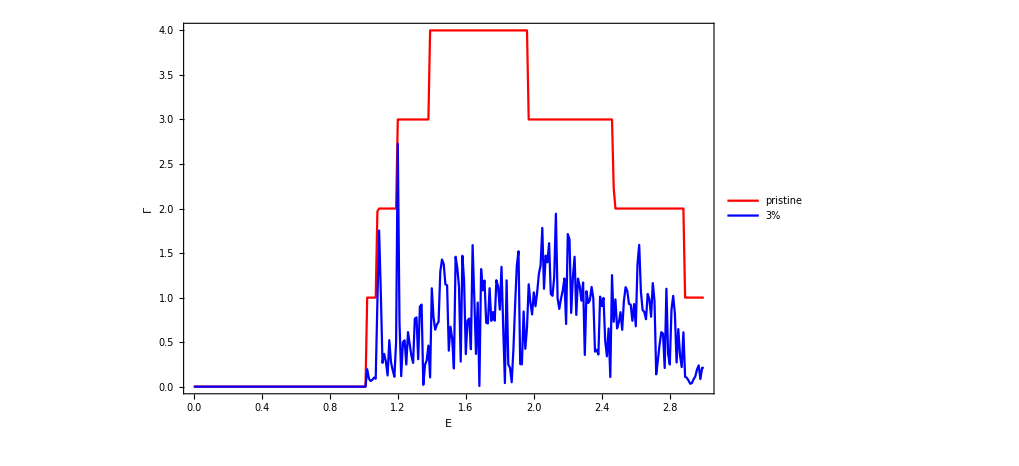

```mathematica
ListLinePlot[{Table[{ω,pris[ω,0.0001,1,1,-0.75,9]},{ω,Range[0,3,0.01]}],Table[{ω,device[ω,0.0001,1,0.5,9,212]},{ω,Range[0,3,0.01]}]},Frame->True,PlotStyle->{Red,Blue},FrameLabel->{{Γ,None},{Ε,None}},PlotLegends->Placed[{"pristine","3%"},{{0.2,0.8}}],LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

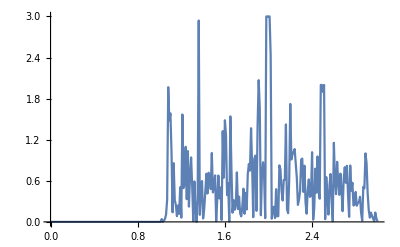

```mathematica
ListPlot[%30,Joined->True,PlotRange->All]
```

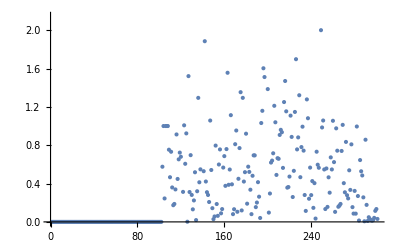

```mathematica
ListPlot[%137]
```

```mathematica
device[ω_,δ_,t_,ϵ_,m_,a_,b_]:=Module[{},
list={RandomSample[Join[Table[unita[ω,δ,t,-0.75,1,ϵ,1],a],(*Table[unitb[ω,δ,t,-0.75,1,ϵ,1],25] ,*)Table[β[ω,δ,t,-0.75,1,9],100-a]]]};
sl1= Module[{J=SL[ω,δ,t,-0.75,1,m]},Do[J=Inverse[IdentityMatrix[2m]-Inverse[list[[1,ζ]]].ConjugateTranspose[T1[1,m]].J.T1[1,m]].Inverse[list[[1,ζ]]],{ζ,1,100}];
 J=J];
il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,1,-0.75,m].ConjugateTranspose[ρ[1,m]]].sl1;
ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,1,-0.75,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,t,1,-0.75,m];gdd1:=il1-ConjugateTranspose[il1];grr1:= ir1-ConjugateTranspose[ir1];Gnonlocal1:= SR[ω,δ,t,1,-0.75,m].ρ[1,m].il1;GNON1:=Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];If[tr1>pris[ω,0.0001,1,-0.75,1,9],pris[ω,0.0001,1,-0.75,1,9],tr1]]
```

```mathematica
Clear[tr,tr1]
```

```mathematica
device[1.2,0.0001,1,0.5,9,40,0]
```

0.281174

working on 10

working on 20

working on 30

working on 40

working on 50

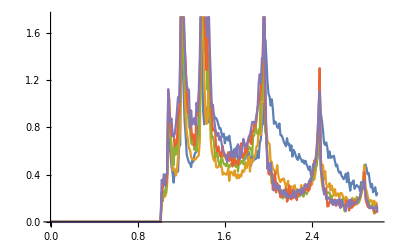

```mathematica
ListLinePlot[Table[Print["working on "<>ToString[num]<>""];Table[{ω,Mean[ParallelTable[device[ω,0.0001,1,150,9,num,0],100]]},{ω,Range[0,3,0.01]}],{num,10,50,10}]]
```

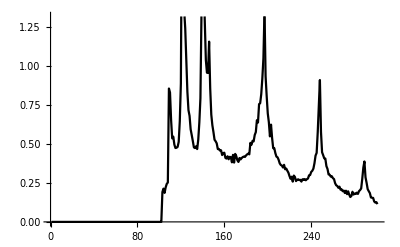

```mathematica
ListPlot[%108,Joined->True,PlotStyle->Black]
```

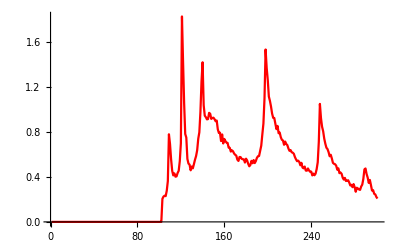

```mathematica
ListPlot[%103,Joined->True,PlotStyle->Red]
```

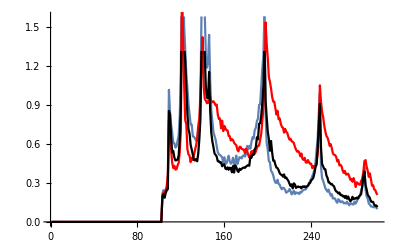

```mathematica
Show[%102,%106,%112]
```

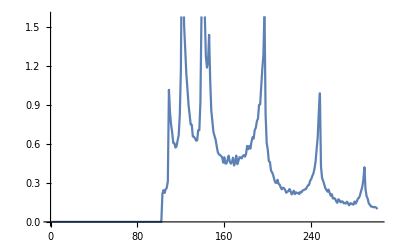

```mathematica
ListPlot[%100,Joined->True]
```

```mathematica
Table[Print["working on "<>ToString[a]<>""];Export["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[a]<>"_0.5.dat",Table[{ω,Mean[ParallelTable[device[ω,0.0001,1,0.5,9,a,0],500]]},{ω,Range[0,3.5,0.01]}]],{a,Range[10,80,5]}]
```

```mathematica
CA=Table[Import["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[x]<>"_vac.dat"],{x,Range[10,70,10]}]
```

{{{-3.,0.000378278},{-2.99,0.000450874},{-2.98,0.000656547},{-2.97,0.000916178},{-2.96,0.00159303},{-2.95,0.0032898},{-2.94,0.139154},{-2.93,0.12427},{-2.92,0.116288},{-2.91,0.120353},{-2.9,0.113196},{-2.89,0.131868},{-2.88,0.115839},{-2.87,0.128208},{-2.86,0.148254},{-2.85,0.141412},{-2.84,0.14897},568,{2.85,0.144851},{2.86,0.139901},{2.87,0.131778},{2.88,0.126764},{2.89,0.122791},{2.9,0.119549},{2.91,0.120562},{2.92,0.113154},{2.93,0.124115},{2.94,0.139179},{2.95,0.00352395},{2.96,0.00150488},{2.97,0.000864057},{2.98,0.000741185},{2.99,0.000477352},{3.,0.000393072}},6}
 |  |  |  |

```mathematica
Dimensions[%48]
```

{7,601,2}

```mathematica
misfit16[n_,x_,y_]:=Module[{m5=Transpose[Join[{Range[-3,3,0.01]},{input[[n]]}]]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-CA[[ξ]][[1;;601,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,7}]; 
Transpose[Join[{Range[10,70,10]},{ρ1}]]]
```

```mathematica
ListLinePlot[Transpose[Join[{Range[-3,3,0.01]},{input[[2]]}]]]
```

```mathematica
Table[ListLinePlot[Transpose[Join[{Range[-3,3,0.01]},{input[[n]]}]]],{n,100}]
```